### One Dimension Prolate Spheroidal Wave Functions Hamed Baghal Ghaffari Date: 2020-05-14

```mathematica
prolate[m_,c_]:=(
M=ConstantArray[0,{m,m}];
M[[1,1]]=4*Pi^2*c^2*(1/3);M[[1,3]]=8*Pi^2*c^2/(3*Sqrt[5]); 
M[[3,1]]=8*Pi^2*c^2/(3*Sqrt[5]);
For[i=1,i≤m-3,i++,
M[[i+1,i+3]]=4*Pi^2*c^2*(i+2)*(i+1)/((2*i+3)*Sqrt[(2*i+5)*(2*i+1)]);
];
For[i=1,i≤m-1,i++,
M[[i+1,i+1]]=(i+1)*i+4*Pi^2*c^2*(2*i^2+2*i-1)/((2*i+3)*(2*i-1));
];
For[i=1,i≤m-3,i++,
M[[i+3,i+1]]=4*Pi^2*c^2*(i+2)*(i+1)/((2*i+3)*Sqrt[(2*i+5)*(2*i+1)]);
];
Return[N[M]]
)
```

```mathematica
prolate[5,1]//MatrixForm
```

```mathematica
({{13.15947253478581, 0., 11.770190054329014, 0., 0.}, {0., 25.68705056261446, 0., 10.337876399374007, 0.}, {11.770190054329014, 0., 26.67917112609199, 0., 10.088734332282014}, {0., 10.337876399374007, 0., 32.177857886671575, 0.}, {0., 0., 10.088734332282014, 0., 39.99556216324597}})
```

{{13.1595,0.,11.7702,0.,0.},{0.,25.6871,0.,10.3379,0.},{11.7702,0.,26.6792,0.,10.0887},{0.,10.3379,0.,32.1779,0.},{0.,0.,10.0887,0.,39.9956}}

```mathematica
coefficientprolate[m_,c_,n_]:=(
M=prolate[m,c];
{eigs,vecs}=N[Eigensystem[M]];
     list1=Partition[Riffle[eigs,vecs],2];
     list2=Sort[list1,#1[[1]]<#2[[1]]&];
Return[list2[[n,2]]]
)
```

```mathematica
coefficientprolate[4,1,1]
```

{0.865456,0.,-0.500985,0.}

```mathematica
PSWF[x_,m_,c_,n_]:=(
y=0;
w=coefficientprolate[m,c,n];
For[i=1,i≤m,i++,
y=y+w[[i]]*LegendreP[i-1,x]*Sqrt[i-1/2];
];
Return[N[y]]
)
```

```mathematica
PSWF[1/4,50,Pi,1]
```

-0.862566

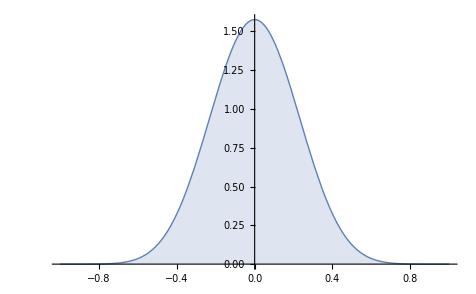

```mathematica
Plot[-PSWF[x,50,Pi,1],{x,-1,1},Filling->Bottom,PlotStyle->Thick]
```

```mathematica
finitefourierlegendre[x_,c_,n_]:=(
If[
x==0,If[n==0,y=Sqrt[2],y=0]
];
If [
c==0,If[n==0,y=Sqrt[2],y=0]
];
If [
x>0,If[c>0,y=(Sqrt[n+1/2]*I^n)/Sqrt[c*x]*BesselJ[n+1/2,2*Pi*c*x]]
];
Return[N[y]]
)
```

```mathematica
finitefourierlegendre[.5,1,2]
```

-0.961217

```mathematica
finitePSWF[x_,m_,c_,n_]:=(
y=0;
w=coefficientprolate[m,c,n];
For[i=1,i≤m,i++,
y=y+w[[i]]*finitefourierlegendre[x,c,i-1];
];
Return[N[y]]
)
```

```mathematica
finitePSWF[.5,50,1,2]
```

3.83381×10^-20+0.992883 ⅈ

```mathematica
finitePSWF[1,100,1,1]
```

0.0185115+2.66188×10^-18 ⅈ

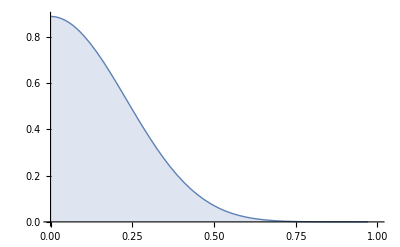

```mathematica
Plot[-finitePSWF[x,50,Pi,1],{x,0,1},Filling->Bottom,PlotStyle->Thick]
```

```mathematica
Plot[(Abs[finitePSWF[x,40,1,1]])/(PSWF[x,40,1,1]),{x,0,1},Filling->Bottom,PlotStyle->Thick]
```

-Graphics-